# The Cartesian oval collimator

In geometry, a Cartesian oval, named after René Descartes, is a plane curve, the set of points that have the same linear combination of distances from two fixed points.
As Descartes discovered, Cartesian ovals may be used in lens design. By choosing the ratio of distances from ta and tb to match the ratio of sines in Snell’s law, and using the surface of revolution of one of these ovals. The Fermat principle it predicts that the optical path of the axial ray is equal to the path of any non-axial ray.

```mathematica
-ta+n tb==Sqrt[(za-ta)^2+ra^2]+n Sqrt[(tb-za)^2+ra^2]
```

Where,  ta is the first point, tb is the second point,  n is the refraction index, ra is the independent variable and za is the profile of the Cartesian oval.  If we take tb to tend to infinity we have a Cartesian oval collimator

```mathematica
Limit[-ta+n tb-(Sqrt[(za-ta)^2+ra^2]+n Sqrt[(tb-za)^2+ra^2]),tb->Infinity]
```

-ta-√(ra^2+(ta-za)^2)+n za

Solving for za, we get the profile of the Cartesian oval collimator, where ra is the independent variable on the horizontal axis

```mathematica
PosibleSolutions=FullSimplify[Solve[0==-ta-√(ra^2+(ta-za)^2)+n za,za]]
```

{{za→((-1+n) ta-√((-1+n^2) ra^2+(-1+n)^2 ta^2))/(-1+n^2)},{za→((-1+n) ta+√((-1+n^2) ra^2+(-1+n)^2 ta^2))/(-1+n^2)}}

So for lets put the refraction index as n=1.5 and the focus at ta=-20.

```mathematica
PosibleSolution1=za/.((PosibleSolutions[[1]])/.ta->-20)/.n->1.5;
```

```mathematica
PosibleSolution2=za/.((PosibleSolutions[[2]])/.ta->-20)/.n->1.5;
```

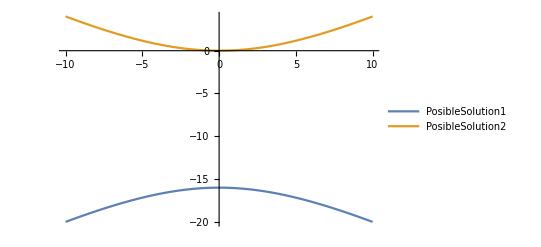

```mathematica
Show[Plot[{PosibleSolution1,PosibleSolution2},{ra,-10,10},PlotLegends->"Expressions"],PlotRange->All]
```

From the figure we can see that the plots that is correct is the Possible solution 2 because where is placed the other solution is no scenes.

We get two solution where one of the solutions is valid for positive refraction index, to know which solution is the right we plot them.

Now it is time, to focus on the ray tracing, for that we recall the Snell’s law

So to get the unity vector with the direction of the refraction we use the Snell law and feet it with the following vector, where the first one is the ray form the object to the surface and the second one is the normal vector of the surface.

```mathematica
v1={ra/(√((ra)^2+(za[ra,n,ta]-ta)^2)),(za[ra,n,ta]-ta)/(√((ra)^2+(za[ra,n,ta]-ta)^2)),0};
na={dza[ra,n,ta]/(√((dza[ra,n,ta])^2+1)),-1/(√((dza[ra,n,ta])^2+1^2)),0};
```

Where, dza is the derivative of a with respect to  za. So with the Snell’s law we have,

```mathematica
(1/n)FullSimplify[Cross[na,FullSimplify[Cross[-na,v1]]]]-na Sqrt[1-(1/n^2)FullSimplify[Cross[na,v1]].FullSimplify[Cross[na,v1]]]
```

{(ra+dza[ra,n,ta] (-ta+za[ra,n,ta]))/(n (1+dza[ra,n,ta]^2) √(ra^2+(ta-za[ra,n,ta])^2))-(dza[ra,n,ta] √(1-(ra+dza[ra,n,ta] (-ta+za[ra,n,ta]))^2/(n^2 (1+dza[ra,n,ta]^2) (ra^2+(ta-za[ra,n,ta])^2))))/(√(1+dza[ra,n,ta]^2)),(dza[ra,n,ta] (ra+dza[ra,n,ta] (-ta+za[ra,n,ta])))/(n (1+dza[ra,n,ta]^2) √(ra^2+(ta-za[ra,n,ta])^2))+(√(1-(ra+dza[ra,n,ta] (-ta+za[ra,n,ta]))^2/(n^2 (1+dza[ra,n,ta]^2) (ra^2+(ta-za[ra,n,ta])^2))))/(√(1+dza[ra,n,ta]^2)),0}

Where the components of the solution we are going to called as ra1 and za1. Therefore, for plotting proposes we have,

```mathematica
za[ra_,n_,ta_]:=((-1+n) ta+√((-1+n^2) ra^2+(-1+n)^2 ta^2))/(-1+n^2);
dza[ra_,n_,ta_]:=Module[{a},a=ra/(√((-1+n^2) ra^2+(-1+n)^2 ta^2))];
ra1[ra_,n_,ta_]:=Module[{t},t=(ra+(-ta+za[ra,n,ta]) dza[ra,n,ta])/(n √(ra^2+(ta-za[ra,n,ta])^2) (1+(dza[ra,n,ta])^2))-(dza[ra,n,ta] √(1-(ra+(-ta+za[ra,n,ta]) dza[ra,n,ta])^2/(n^2 (ra^2+(ta-za[ra,n,ta])^2) (1+(dza[ra,n,ta])^2))))/(√(1+(dza[ra,n,ta])^2))];
za1[ra_,n_,ta_]:=Module[{t},t=(dza[ra,n,ta] (ra+(-ta+za[ra,n,ta]) dza[ra,n,ta]))/(n √(ra^2+(ta-za[ra,n,ta])^2) (1+(dza[ra,n,ta])^2))+(√(1-(ra+(-ta+za[ra,n,ta]) dza[ra,n,ta])^2/(n^2 (ra^2+(ta-za[ra,n,ta])^2) (1+(dza[ra,n,ta])^2))))/(√(1+(dza[ra,n,ta])^2))];
```

Now we defined the Range in which we are going to plot the Cartesian Oval

```mathematica
rmax=15;
```

In this section is the ray tracing of the code, we plot the normal, tangential vector and the cosine directors, and uu is the plot of the unity vector by its components ra1 and za1.

```mathematica
l[ra_,n_,ta_]:=Module[{t},t=Graphics[Line[{{0, ta},{ra,za[ra,n,ta]},{ra,20}}]]];
uu[ra_,n_,ta_]:=Module[{t},t=Graphics[{Thick,Red,Line[{{ra,za[ra,n,ta]},{ra+ra1[ra,n,ta],za[ra,n,ta]+za1[ra,n,ta]}}]}]];
```

We also want to plot the normal vector and tangential vector of the surface of the Cartesian oval, therefore we defined the following unity vectors:

```mathematica
nor[ra_,n_,ta_]:=Module[{t1},t1=Graphics[{Thick,Dashed,Green,Line[{{ra+dza[ra,n,ta]/Sqrt[(dza[ra,n,ta])^2+1],za[ra,n,ta]-1/Sqrt[(dza[ra,n,ta])^2+1]},{ra-dza[ra,n,ta]/Sqrt[(dza[ra,n,ta])^2+1],za[ra,n,ta]+1/Sqrt[(dza[ra,n,ta])^2+1]}}]}]];
tan[ra_,n_,ta_]:=Module[{t1},t1=Graphics[{Thick,Dashed,Blue,Line[{{ra-1/Sqrt[(dza[ra,n,ta])^2+1],za[ra,n,ta]-dza[ra,n,ta]/Sqrt[(dza[ra,n,ta])^2+1]},{ra+1/Sqrt[(dza[ra,n,ta])^2+1],za[ra,n,ta]+dza[ra,n,ta]/Sqrt[(dza[ra,n,ta])^2+1]}}]}]];
```

Here in this section is the manipulation of the Cartesian oval collimator

```mathematica
Quiet[Manipulate[Show[Plot[{za[ra,n,ta]},{ra,-rmax,rmax},PlotStyle->{Black},AspectRatio->Automatic,AxesLabel->{r,z},Filling->20,PlotLabel->"Red=cosine directors, Blue/Green=tangencial/normal vectors"],Table[{l[i,n,ta],l[-i,n,ta],uu[i,n,ta],nor[i,n,ta],tan[i,n,ta],uu[-i,n,ta],nor[-i,n,ta],tan[-i,n,ta]},{i,-gg,g,gg}],PlotRange->{{-25,25},{-60,20}}],{{n,1.5,"Refraction index: n"},1.5,3},{{ta,-50,"Focus: ta"},-50,-1},{{g,8,"Lines"},-15,15},{{gg,2,"Space beetwen lines"},2,4}]]
```